## Lesson 12: Repeated characteristic roots

## Overview

Now that the course has covered repeated roots and complex roots, the final case is when there is the same repeated root in the characteristic equation.

When roots are repeated, λ can only take one value, which only produces one solution to the differential equation.

Discovering the second solution requires a technique invented by the mathematician Jean d’Alembert.

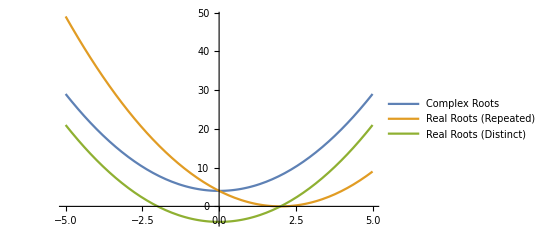

```mathematica
Plot[{x^2+4,x^2-4x+4,x^2-4},{x,-5,5},]
```

## Repeated Roots

Consider again the constant coefficient linear homogeneous second-order differential equation:

a y''(x)+b y'(x)+c y(x)=0

When the function y(x) is replaced by y(x) = e^(λ x), the characteristic equation is produced:

a λ^2+b λ + c=0

When the roots are repeated, the discriminant is zero and the result is:

λ=-b/(2a)

Thus there is one solution:

y_1(x)=e^(-b/(2 a)x)

However, the second solution, y_2(x), remains unknown.

D’Alembert solved equations of this type by assuming the solution was of the form u(x)e^(λ x) and then solving for u(x) so that it would satisfy the differential equation.

## Find the Unknown Solution

Begin by substituting y(x)=u(x)e^(λ x) into the differential equation:

```mathematica
eqn=(a y''[x]+b y'[x]+c y[x]==0)/.y->Function[x,u[x]Exp[λ x]]
```

c ⅇ^(x λ) u[x]+b (ⅇ^(x λ) λ u[x]+ⅇ^(x λ) u'[x])+a (ⅇ^(x λ) λ^2 u[x]+2 ⅇ^(x λ) λ u'[x]+ⅇ^(x λ) u''[x])==0

Assuming that λ is a root to the characteristic equation, simplify the equation:

```mathematica
Assuming[a λ^2+b λ +c==0,FullSimplify[eqn]]
```

(b+2 a λ) u'[x]+a u''[x]==0

λ is a repeated root and thus occurs when λ=-b/(2a):

```mathematica
(b+2 a λ) u'[x]+a u''[x]==0/.{λ->-b/(2a)}
```

a u''[x]==0

Now you can see that the only condition this unknown function must satisfy is that the second derivative is zero.

## Find the Unknown Solution

Because the second derivative is everywhere zero, this function has no change in its concavity, so it must be a straight line:

```mathematica
DSolveValue[u''[x]==0,u[x],x]
```

C[1]+x C[2]

Verify that if u(x) is of the form α+β x, the function u(x)e^(λ x) is a solution to the differential equation:

```mathematica
eqn=(a y''[x]+b y'[x]+c y[x]==0)/.y->Function[x,(α+β x)Exp[λ x]]
```

c ⅇ^(x λ) (α+x β)+b (ⅇ^(x λ) β+ⅇ^(x λ) (α+x β) λ)+a (2 ⅇ^(x λ) β λ+ⅇ^(x λ) (α+x β) λ^2)==0

Simplify the differential equation assuming that λ is a root of the characteristic equation:

```mathematica
Assuming[a λ^2+b λ +c==0,FullSimplify[eqn]]
```

β (b+2 a λ)==0

When λ is a repeated root, λ=-b/(2a), which gives:

```mathematica
(β (b+2 a λ)==0)/.λ->-b/(2 a)
```

True

## Find the Unknown Solution

Thus, the general solution to the repeated roots problem becomes:

y(x)=C_1 e^(λ x)+C_2(α+β x)e^(λ x)

Because C_1, C_2, α, β are all arbitrary constants, this can be reformulated as:

y(x)=C_1 e^(λ x)+C_2 x e^(λ x)

Verify the result using the Wronskian Determinant theorem:

```mathematica
Wronskian[{Exp[λ x],x Exp[λ x]},x]
```

ⅇ^(2 x λ)

The Wronskian Determinant is nonzero, so the functions form a fundamental solution set.

## Example 1: Repeated Roots Solution

Solve the linear second-order homogeneous differential equation with constant coefficients:

y''(x)+4 y'(x)+4 y(x)=0

y(0)=1

y'(0)=3

Use Roots to solve the characteristic equation:

```mathematica
Roots[4+4λ+λ^2==0,λ]
```

λ==-2||λ==-2

Observe that the roots of the characteristic equation are repeated, so that the solution must be of the form:

```mathematica
ySol[x_]:=Subscript[C, 1] Exp[-2 x] + Subscript[C, 2] x Exp[-2 x]
```

Next, you need to solve for the arbitrary constants so that the function satisfies the initial conditions:

```mathematica
eqn1=ySol[0]==1
```

C_1==1

```mathematica
eqn2=ySol'[0]==3
```

-2 C_1+C_2==3

Solve the system of equations for the constants C_1 and C_2:

```mathematica
constants=Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}][[1]]//Simplify
```

{C_1→1,C_2→5}

Substituting these constants into the general solution gives the solution to the initial value problem:

```mathematica
ySol[x]/.constants
```

ⅇ^(-2 x)+5 ⅇ^(-2 x) x

## Example 1: Repeated Roots Solution

Verify the solution:

```mathematica
solution=ySol[x]/.constants
```

ⅇ^(-2 x)+5 ⅇ^(-2 x) x

Substitute the solution into the equation to show it satisfies the equation:

```mathematica
(y''[x]+4y'[x]+4y[x]==0)/.y->Function[x,Evaluate[solution]]//Simplify
```

True

Verify the initial conditions:

```mathematica
(solution==1)/.x->0
```

True

```mathematica
(D[solution,x]==3)/.x->0
```

True

The solution found satisfies the differential equation and the initial conditions.

Comparing this to the output produced by DSolveValue, you can see that they are exactly equal:

```mathematica
sln=DSolveValue[{y''[x]+4y'[x]+4y[x]==0,y[0]==1,y'[0]==3},y[x],x]//Expand
```

ⅇ^(-2 x)+5 ⅇ^(-2 x) x

## Example 2: Repeated Roots Solution

Solve the linear second-order homogeneous differential equation with constant coefficients:

y''(x)-6 y'(x)+9 y(x)=0

y(0)=-1

y'(0)=1/2

First, use Roots to solve the characteristic equation:

```mathematica
Roots[9-6λ+λ^2==0,λ]
```

λ==3||λ==3

You can see that the roots of the characteristic equation are repeated, so that the solution must be of the form:

```mathematica
ySol[x_]:=Subscript[C, 1] Exp[3 x]+Subscript[C, 2] x Exp[3 x]
```

Next, you need to solve for the arbitrary constants so that the function satisfies the initial conditions:

```mathematica
eqn1=ySol[0]==-1
eqn2=ySol'[0]==1/2
```

C_1==-1

3 C_1+C_2==1/2

Solve the system of equations for the constants C_1 and C_2:

```mathematica
constants=Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}][[1]]//Simplify
```

{C_1→-1,C_2→7/2}

Thus, the solution must be:

```mathematica
ySol[x]/.constants
```

-ⅇ^(3 x)+7/2 ⅇ^(3 x) x

## Example 2: Repeated Roots Solution

Verify the solution:

```mathematica
solution=ySol[x]/.constants
```

-ⅇ^(3 x)+7/2 ⅇ^(3 x) x

Substitute the solution into the equation:

```mathematica
(y''[x]-6y'[x]+9y[x]==0)/.y->Function[x,Evaluate[solution]]//Simplify
```

True

Verify the initial conditions:

```mathematica
(solution==-1)/.x->0
```

True

```mathematica
(D[solution,x]==1/2)/.x->0
```

True

The solution found satisfies the differential equation and the initial conditions.

Comparing this to the output produced by DSolveValue, you can see that they are exactly equal:

```mathematica
sln=DSolveValue[{y''[x]-6y'[x]+9y[x]==0,y[0]==-1,y'[0]==1/2},y[x],x]//Expand
```

-ⅇ^(3 x)+7/2 ⅇ^(3 x) x

## Summary of Constant Coefficients

For any equation with the form:

a y''(x)+b y'(x)+c y(x)=0

you can use the previous results of the past four lessons to find the solution for any values of a, b and c.

To summarize, solutions to the preceding differential equation can be completely described by solutions to the associated characteristic equation.

The characteristic equation is derived by assuming y(x)=e^(λ x).

## Summary of Constant Coefficients

Using y(x)=e^(λ x) in the differential equation gives the characteristic equation:

```mathematica
(a y''[x]+b y'[x]+c y[x]==0)/.y->Function[x,Exp[λ x]]//Factor
```

ⅇ^(x λ) (c+b λ+a λ^2)==0

Thus, to know solutions to the differential equation is to know solutions to the quadratic polynomial.

Let λ_1,λ_2 denote the roots of said characteristic polynomial.

When λ_1≠λ_2 and both are real valued, the solution takes the form:

y(x)=C_1 e^(λ_1 x)+C_2 e^(λ_2 x)

When λ_1≠λ_2 and both are complex valued (λ=r±ⅈ γ), the solution takes the form:

y(x)=e^(r x)(C_1 cos(γ x)+C_2 sin(γ x))

## Summary of Constant Coefficients

As proven in this lesson, when λ_1=λ_2, there is a real repeated root and this has a solution of the form:

y(x)=C_1 e^(λ_1 x)+C_2 x e^(λ_1 x)

D’Alembert found a clever way of finding solutions to complex forms of differential equations by assuming that solutions would look like u(x)e^(λ x) and solving for u(x).

This method is not only applicable when there are repeated roots in the characteristic equation but can also be used to solve many equations of many different forms.